```mathematica
k=0.07
sec[r_]:=Sqrt[1+(-10*E^(-k*r^2)*k*r)^2]
angle[r_]:=0.5*(Sqrt[sec[r]]-1)
```

0.07

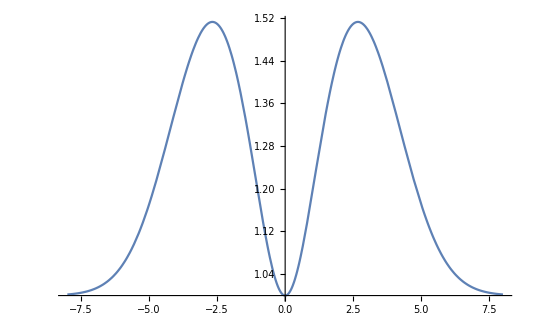

```mathematica
Plot[sec[r],{r,-8,8}]
```

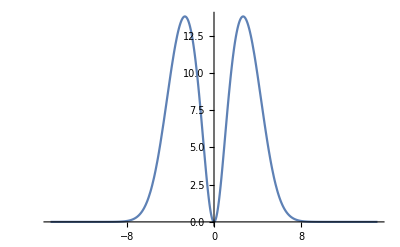

```mathematica
Plot[angle[r]*120,{r,-15,15}]
```